# Exploring Representation Theory and Quantum information

"The law of comparative advantage says that  the more different you are from other people, the more valuable you are economically." - David Deutsch

Inspired by a course on algorithms, many, many discussions with a physicist (also a partner) and an elegant explanation of why  infinite-dimensional fields of QFT are necessary, I developed interest in this field and sought to create a notebook for building an understanding of representation theory in quantum information

## Representation theory introduction

Representation has lots of interesting things: as quantum information theorists, perhaps few things would be more interesting that the Schur-Weyl duality. This arises due to a neat fact that a "vector space can be interpreted either as a representation of a group or as state-space of a quantum system" [AW. Harrow].  In this section, we will explore some basics through code and get a feel of the field. Note: This notebook follows the structure and definitions from [AW. Harrow].

## Basics 1. Understanding representations

For a complex vector space V , we can define an endomorphism End(V) , that is, a set of linear maps from V to itself. A representation of a group G is a vector space V together with a homomorphism from G to End(V ). Homomorphism is a fancy way of saying that this map is a function R : G → End(V ) such that R(g1)R(g2) = R(g1g2). If R(g) is a unitary operator for all g, then we say R is a unitary representation. A note on endomorphisms: They need not span the entire space, they should be linear and be defined for the entire vector space.

```mathematica
d = 3;(* dim V *)
Clear[R];
basisV = IdentityMatrix[d];   (* columns are basis vectors e1,e2,e3 *)
EM[i_, j_] := SparseArray[{i, j} -> 1, {d, d}];  (* Endomorphism basis, E_ij has a 1 at (i,j), 0 else - standard definition but something else could have been used *)
basisEndV = Flatten[Table[EM[i, j], {i, d}, {j, d}], 1];
(* Check the size of these bases *)
dimV = d;
dimEndV = Length[basisEndV];   (* should be d^2 *)
{dimV, dimEndV}
(* Reconstruct any linear map A in End(V) from the E_ij basis *)
A = RandomComplex[NormalDistribution[0, 1], {d, d}];  (* a random endomorphism *)
reconstructA = Sum[A[[i, j]] EM[i, j], {i, d}, {j, d}];
Simplify[reconstructA == A]   (* True: the {E_ij} form a basis of End(V) *)
G = SymmetricGroup[3];
elems = GroupElements[G];
toList[g_] := PermutationList[g, d];
compose[p_, q_] := p[[q]];
(* Representation map R: permutation list -> permutation matrix (d x d) *)
R[p_List] := Table[If[j == p[[i]], 1, 0], {i, d}, {j, d}];
(* Check the homomorphism property: R(g1 g2) = R(g1) R(g2) *)
permLists=toList/@GroupElements[SymmetricGroup[d]];
testPairs=Flatten[Table[{permLists[[i]],permLists[[j]]},{i,Length[permLists]},{j,Length[permLists]}],1];
homomorphismChecks=Map[Function[pair,With[{p=pair[[1]],q=pair[[2]]},Simplify[R[compose[p,q]]===R[p].R[q]]]],testPairs];
AllTrue[homomorphismChecks,TrueQ];
idPerm=Range[d];
idCheck=R[idPerm]===IdentityMatrix[d];
inverseCheck=AllTrue[permLists,Function[p,With[{inv=Ordering[p]},R[inv].R[p]===IdentityMatrix[d]&&R[p].R[inv]===IdentityMatrix[d]]]];
{idCheck,inverseCheck};
ConjugateTranspose[R[{2,3,1}]].R[{2,3,1}] === IdentityMatrix[d]
unitaryQ[m_] := ConjugateTranspose[m].m === IdentityMatrix[Length[m]];
unitaryChecks = unitaryQ /@ (R /@ permLists);
AllTrue[unitaryChecks, TrueQ]
```

{3,9}

True

True

True

Now let us say you have two vector spaces V1 and V2, then we can define a homomorphism Hom(V1,V2) to be the set of linear transformations from V1 to V2. Let us say that we have a group G that acts on V1 and V2 with representation matrices R1 and R2 (i.e. different homomorphisms as discussed above in the definition of representations). We can ask how would the group G then act on the Hom(V1,V2) itself, that is, we want to define a representation of G on the space Hom(V1, V2). as we already know, a representation itself is an homomorphism, meaning that that two below actions should be equivalent : 

1) moving a vector in V1 under action of G via R1 and then applying a transformation M ∈ Hom(V1,V2) 
2) Applying transformation M and then moving output vector from V2 under the action of G via R2

Through this equivalence we see that the representation of the group G on Hom(V1, V2) is given by the map from M to R2(g)MR1(g)^−1 for any M ∈ Hom(V1, V2). 

Now, for any representation (R, V , we define V_G to be the space of G-invariant vectors of V : i.e. V_G := {|v⟩ ∈ V : R(g)|v⟩ = |v⟩ ∀g ∈ G}. Of particular interest is the space Hom(V1, V2)_G, which can be thought of as the linear maps from V1 to V2 which commute with the action of G. Formally, this means M∘R_1(g)=R_2(g)∘M
If Hom(V1,V2)G contains any invertible maps (or equivalently, any unitary maps) then we say that (R1, V1) and (R2, V2) are equivalent representations. 

To be clearer, assume you have an M such that g.M=M, such an invariant M is called an intertwiner. we already know from previous para that g.M = R2(g)MR1(g)^−1 = M -> R2M=MR1, of course for this we should also be able to write R2=MR1M^-1 and hence M has to be invertible! 

In the below code snippet, I visualize the definitions above for addition mod 2 group. I show two representations R1​ and R2​ on C2 are related by an intertwiner. The code checks that both R1​ (a reflection) and R2​ (a swap) are valid representations, constructs the canonical group action on Hom(V1​,V2​), solves for invariant maps M satisfying R2​(g)M=MR1​(g), and finds an invertible intertwiner T showing the two representations are equivalent. Finally, it identifies each representation’s invariant subspace and confirms that T maps one invariant line to the other, preserving the group symmetry.

```mathematica
(* ----- Setup: the group G = {e, g} ----- *)
ClearAll[R1, R2, g, e];
d = 2;  (* dimension of V1, V2 *)
(* Two representations R1 and R2 of G on C^2 *)
(* R1(g) = diag(1,-1) (reflection in 2nd coordinate) *)
R1[e] = IdentityMatrix[d];
R1[g] = {{1, 0}, {0, -1}};
(* R2(g) = Swap matrix (permutes the two coordinates) *)
R2[e] = IdentityMatrix[d];
R2[g] = {{0, 1}, {1, 0}};
(* Check: both are homomorphisms of groups *)
R1[g].R1[g] === R1[e]
R2[g].R2[g] === R2[e]
(* ----- Canonical action of G on Hom(V1,V2) ----- *)
ClearAll[a, b, c, dM];
M = {{a, b}, {c, dM}};  (* generic linear map V1 -> V2 *)
(* canonical action: g·M = R2(g) M R1(g)^(-1) *)
act[e_, X_] := R2[e].X.Inverse[R1[e]];
act[g_, X_] := R2[g].X.Inverse[R1[g]];
(* compute g·M explicitly *)
gActM = Simplify[act[g, M]];
gActM // MatrixForm
(* ----- Solve for intertwiners: R2(g) M == M R1(g) ----- *)
eqs = Thread[gActM == M];                 (* elementwise equations *)
sol = Solve[Flatten[eqs], {a, b, c, dM}]  (* parameterization of all intertwiners *)
(* general G-invariant map M (Hom(V1,V2)^G) *)
Mint[a_, b_] := {{a, b}, {a, -b}};
Mint[a, b] // MatrixForm
(* determinant of M to check invertibility *)
Det[Mint[a,b]]  (* = -2 a b *)
(* pick a concrete invertible intertwiner, e.g., a=1, b=1 *)
T = Mint[1, 1];
Det[T]            (* should be -2 ≠ 0, so invertible *)
T // MatrixForm
(* verify intertwining condition R2(g) T == T R1(g) *)
Simplify[R2[g].T == T.R1[g]]
(* prove equivalence: T^{-1} R2(g) T == R1(g) for all g *)
Simplify[Inverse[T].R2[g].T == R1[g]]
(* ----- Invariant subspaces (V^G) ----- *)
ClearAll[x, y];
v = {x, y};
(* Invariants in V1: R1(g) v == v *)
Solve[R1[g].v == v, {x, y}]
(* => {x arbitrary, y = 0} so V1^G = span{(1,0)} *)
(* Invariants in V2: R2(g) v == v *)
Solve[R2[g].v == v, {x, y}]
(* => {x = y}, so V2^G = span{(1,1)} *)
(* Check T maps invariant line in V1 to invariant line in V2 (as expected) *)
T.{1, 0}
```

True

True

(c | -dM
a | -b)

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→a,dM→-b}}

(a | b
a | -b)

-2 a b

-2

(1 | 1
1 | -1)

True

True

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→x}}

{1,1}

```mathematica
(* Pick symbolic intertwiner M *)
M0 = {{a, b}, {a, -b}};
(* Check invariance under group action *)
Simplify[ act[g, M0] == M0 ]
```

True

In the below code, we do the same as above but for SU(2) group (do not ask why I thought this was worth doing - its really not that hard to extend your understanding from discrete to continuos groups, but hey, there's no harm in a few extra lines of redundancy!). To recall, we are setting up and displaying the intertwining condition that defines G-equivariant (intertwining maps R2=MR1M^-1) The first two Print lines are just explanatory text: rememeber the canonical action of G on Hom(V1​,V2​) is M↦R2(g)MR1(g)^−. M is G-invariant (an intertwiner) exactly when R2​M=MR1​. The expression invarianceEq is the symbolic matrix R2​M−MR1. invarianceEq // MatrixForm merely shows this residual so you can see the equations entry-by-entry. The actual mathematical check happens when you set those entries to zero and solve for the unknowns. Any solution matrix M produced there satisfies R2​M=MR1​; if one such M is invertible, the code has exhibited an equivalence between the two representations. Formally, this means that there exists a unitary change of basis U : V1 → V2 such that for any g ∈ G, UR1(g)U† = R2(g).

```mathematica
(* Define Pauli matrices *)
σx = {{0, 1}, {1, 0}};
σy = {{0, -I}, {I, 0}};
σz = {{1, 0}, {0, -1}};
(* Define the SU(2) rotation operator *)
R[n_, θ_] := MatrixExp[-I θ/2 (n[[1]] σx + n[[2]] σy + n[[3]] σz)];
(* Choose a group element: rotation by θ around axis n *)
n = Normalize[{1, 1, 1}];
θ = Pi/3;
(* Representations on V1 and V2 *)
R1 = R[n, θ];                     (* Representation on V1 = ℂ^2 *)
R2 = {{1, 0}, {0, 1}}.R[n, θ].{{1, 0}, {0, 1}};   (* You can pick any R2 you want, e.g. same as R1 *)
(* For nontrivial example: R2 = S.R1.Sinv where S is change of basis *)
(* Define S, Sinv to build an equivalent representation *)
S = {{1, 1}, {0, 1}};
Sinv = Inverse[S];
R2 = S.R1.Sinv;
(* Define the space Hom(V1,V2): matrices of shape dim(V2)×dim(V1) *)
(* An arbitrary linear map M ∈ Hom(V1,V2) *)
M = Array[m, {2, 2}];  (* m11, m12, m21, m22 symbolic entries *)
(* Canonical action of G on M *)
ActionOnM[g_] := R2.M.Inverse[R1];
(* Intertwining condition: M invariant under G-action *)
invarianceEq = Simplify[Chop[ActionOnM[g] - M]];
Print["Canonical action of G on Hom(V1,V2): M → R2 M R1^{-1}"];
Print["Check for G-invariance: R2 M = M R1"];
Print["Symbolic condition:"];
invarianceEq // MatrixForm;
(* Solve for all M that satisfy R2 M = M R1 *)
sol = Solve[Thread[Flatten[invarianceEq] == 0], Flatten[M]];
Print["G-invariant intertwiners M:"];
TableForm[sol]
(* If an invertible M exists, the two representations are equivalent *)
If[sol =!= {}, Print["⇒ There exists a nonzero (possibly invertible) intertwiner → equivalent representations."]];
```

Canonical action of G on Hom(V1,V2): M → R2 M R1^{-1}

Check for G-invariance: R2 M = M R1

Symbolic condition:

Solve::svars: Equations may not give solutions for all "solve" variables.

G-invariant intertwiners M:

m[2,1]→1/2 m[1,1]-1/2 m[1,2] | m[2,2]→1/2 ⅈ m[1,1]+(1-ⅈ/2) m[1,2]

⇒ There exists a nonzero (possibly invertible) intertwiner → equivalent representations.

Now, Dual of a vector space V is the set of linear maps from V to C and is denoted V*. Usually if vectors in V are denoted by kets (e.g. |v⟩) then vectors in V* are denoted by bras (e.g. ⟨v|). If we fix a basis {|v1⟩, |v2⟩, . . .} for V then the transpose is a linear map from V to V∗ given by |vi⟩ → ⟨vi|. Now, for a representation (R,V) we can define the dual representation (R*,V*) by R*(g)⟨v*| := ⟨v*|R(g^−1). 

If we think of R* as a representation on V (using the transpose map to relate V and V*), then it is given by R*(g) = (R(g*−1))^ transposed . When R is a unitary representation, this is the same as the conjugate representation R(g)*, where here ∗ denotes the entry wise complex conjugate. One can readily verify that the dual and conjugate representations are indeed representations and that between Hom(V1 , V2 ) and  V1 ⊗ V2 there exists a unitary change of basis such that  for any g ∈ G, UR1(g)U† = R2(g).

```mathematica
(* 1. Define the group, here lets take the addition mod 2, Z2 = {e, g}, g^2 = e  *)
ClearAll[R, Rdual, Rconj, e, g];
group = {e, g};
(* Representation on V = C^2 *)
R[e] = IdentityMatrix[2];
R[g] = {{0, 1}, {1, 0}}; (* swap matrix, unitary *)
(* Helper: group multiplication in Z2 *)
multiply[a_, b_] := If[a === e, b, If[b === e, a, e]];
(* Representation property checker *)
representationQ[rep_] := And @@ Table[
  rep[multiply[a, b]] === rep[a].rep[b],
  {a, group}, {b, group}
  ];
Print["Original representation valid? ", representationQ[R]];
(* 2. Dual and Conjugate Representations  *)
(* Dual: R*(g) = Transpose[R[g^-1]] = Transpose[R[g]] since g=g^-1 in Z2 *)
Rdual[h_] := Transpose[R[h]];
(* Conjugate: R(g)* = entrywise complex conjugate *)
Rconj[h_] := Conjugate[R[h]];
Print["Dual representation valid? ", representationQ[Rdual]];
Print["Conjugate representation valid? ", representationQ[Rconj]];
Print["For unitary R, Rdual == Rconj ? ", Simplify[Rdual[g] == Rconj[g]]];
(* 3. Verify Hom(V1, V2) ≅ V1* ⊗ V2 isomorphism     *)
dimV1 = 2; dimV2 = 3;
basisV1 = IdentityMatrix[dimV1]; (* standard basis vectors |e_i> *)
basisV2 = IdentityMatrix[dimV2];
(* Build the isomorphism Φ : V1* ⊗ V2 -> Hom(V1,V2) *)
(* Φ(v* ⊗ w) acts as x ↦ <v*|x>|w> *)
Phi[vstarTensorW_] := Module[{vstar, w},
  {vstar, w} = vstarTensorW;
  Outer[Times, w, vstar]
  ];
(* Build a complete basis of V1* ⊗ V2 *)
tensorBasis = 
  Flatten[Table[{basisV1[[i]], basisV2[[j]]}, {i, dimV1}, {j, dimV2}], 1];
(* Apply Φ to each basis element -> get a set of matrices in Hom(V1,V2) *)
phiImages = Phi /@ tensorBasis;
(* Flatten into column vectors to build the linear map matrix *)
PhiMatrix = Flatten /@ (Flatten[#, 1] & /@ phiImages);
(* Verify invertibility of Φ as a linear map *)
isInvertible = Det[Transpose[PhiMatrix].PhiMatrix] ≠ 0;
Print["Is Φ invertible (i.e. an isomorphism)? ", isInvertible];
(* 4. Dimension sanity check *)
dimHom = dimV1*dimV2;
dimTensor = dimV1*dimV2;
Print["dim(Hom(V1,V2)) == dim(V1*⊗V2)? ", dimHom == dimTensor];
```

Original representation valid? {True,True}&&{True,True}

Dual representation valid? {True,True}&&{True,True}

Conjugate representation valid? {True,True}&&{True,True}

For unitary R, Rdual == Rconj ? True

Is Φ invertible (i.e. an isomorphism)? True

dim(Hom(V1,V2)) == dim(V1*⊗V2)? True

Now, I introduce the topic of irreducible representations - one of the most important concepts that tell a lot about the symmetric structure of the spaces! first of all, an irreducible representation or an irrep can be thought of as the "atom" of representations of a group on a space and in this sense, it can be used to build other representations. Now  imagine a representation (R, V) such that the only space thats invariant under the action of the group representation is either {0} or V itself - clearly there cannot be a smaller representation thats possible, if you do find another subspace W of V such that it is also invariant under thr action of R, then (R,W) is the true smallest representation, of course provided that nothing smaller exists that's also invariant and not the null set! This "smallest" rep is our irrep for R(g) for all g∈G

{(1 | 0
0 | 1),(0 | 1
1 | 0)}

{{-1,1},{{-1,1},{1,1}}}

(-ⅈ | 0
0 | ⅈ)

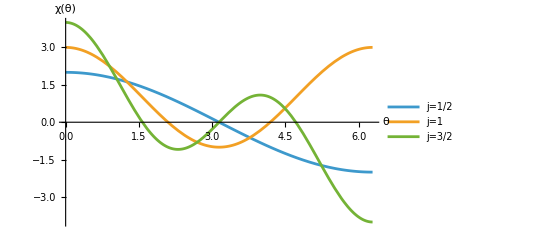

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1)

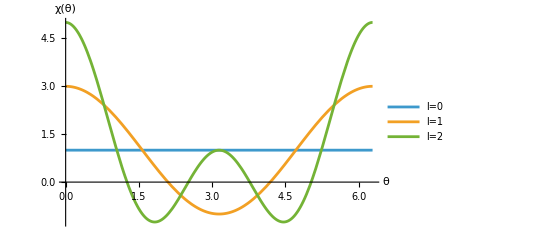

Let G be a group and (R, V) a finite-dimensional representation of G, i.e. a homomorphism R : G → GL(V).  Denote by 𝐺̂ the set of all inequivalent irreducible representations (irreps) of G.  Each irrep is represented by a pair (r_λ, V_λ), where r_λ : G → GL(V_λ) acts irreducibly on V_λ.
 
For any reducible representation (R, V) there exists a basis in which each R(g) takes the block-diagonal form

   R(g) ≅ ⨁_{λ ∈ 𝐺̂} ⨁_{j=1}^{n_λ} r_λ(g)
          = ⨁_{λ ∈ 𝐺̂} ( r_λ(g) ⊗ I_{n_λ} ).
          
Here, n_λ is the multiplicity of the irrep λ in V, I_{n_λ} is the identity on an n_λ-dimensional multiplicity space. The symbol ≅ means that there exists a unitary change of basis relating the left-hand and right-hand sides. This expresses that, under a suitable basis, every R(g) acts in blocks  corresponding to irreducible types; each irrep block may appear multiple times.  Writing r_λ(g) ⊗ I_{n_λ} indicates that the group acts through r_λ(g) on the irrep component and trivially (as the identity) on the multiplicity component.

Correspondingly, the vector space V decomposes as

 V ≅ ⨁_{λ ∈ 𝐺̂} ( V_λ ⊗ ℂ^{n_λ} ).
 
Each term V_λ ⊗ ℂ^{n_λ} is called the isotypic component of type λ. Here, V_λ carries the structure of the irrep r_λ, ℂ^{n_λ} is the multiplicity space labeling the copies of that irrep and the group G acts only on the V_λ factor and trivially on theℂ^{n_λ} factor. This decomposition shows that V can be viewed as a direct sum of “irrep types” multiplied by the number of times they appear.

The multiplicity space ℂ^{n_λ} can be identified with the space of G-equivariant linear maps from V_λ to V:

 ℂ^{n_λ} ≅ Hom(V_λ, V)^G.
 
Hence the equation previously can be rewritten as V ≅ ⨁_{λ ∈ 𝐺̂} ( V_λ ⊗ Hom(V_λ, V)^G ). The dimension of Hom(V_λ, V)^G equals n_λ because each distinct copy of V_λ inside V defines an independent G-equivariant embedding V_λ → V.

There exists a natural linear map φ : A ⊗ Hom(A, B) → B defined by φ(a ⊗ f) = f(a). This canonical map realizes how elements of A ⊗ Hom(A, B) are sent to B, and it provides the explicit correspondence used in the isotypic decomposition.

## Basics 2. Clebsch Gordan decomposition and Fourier transforms in representation theory

Given two representations (R_μ,V_μ) and (R_ν,V_ν) of a group G, their tensor product (R_μ ⊗ R_ν, V_μ ⊗ V_ν) is generally reducible and decomposes as 

V_μ ⊗ V_ν ≅ ⨁_{λ∈Ĝ} V_λ ⊗ Hom(V_λ, V_μ ⊗ V_ν)^G ≅ ⨁_{λ∈Ĝ} V_λ ⊗ ℂ^{M^λ_{μν}}, (using the results from previous para)

where M^λ_{μν} := dim Hom(V_λ, V_μ ⊗ V_ν)^G is the multiplicity of irrep λ in the tensor product (for G = U_d these are the Littlewood–Richardson coefficients).

The unitary Clebsch–Gordan transform U_CG^{μ,ν} is the change of basis that implements this decomposition: it maps the product space V_μ ⊗ V_ν into registers (|λ⟩ ⊗ V_λ ⊗ ℂ^{M^λ_{μν}}), exposing an irrep label λ, an irrep basis vector in V_λ, and a multiplicity label α ∈ Hom(V_λ, V_μ ⊗ V_ν)^G. 

Using Hom(A,B) ≅ A* ⊗ B, α can be viewed as an intertwiner, and the inverse transform is (U_CG^{μ,ν})†(|λ⟩ ⊗ |v_λ⟩ ⊗ |α⟩) = α(|v_λ⟩) ∈ V_μ ⊗ V_ν. 

In implementations, one typically pads the various V_λ to a common dimension (e.g., with ancillas) to realize a single unitary, restricts attention to finitely many λ when Ĝ is infinite, and observes that the algorithmic complexity is concentrated in constructing/handling the multiplicity spaces.


Now, consider the the regular representation of a finite group G. This is a useful representation given by letting each g ∈ G define an orthonormal basis vector |g⟩. The resulting space Span{|g⟩ : g ∈ G} is denoted C[G] and is called the regular representation. The vector space ℂ[G] has basis |g⟩ for g ∈ G, and G acts on it in two independent ways: left multiplication L(g₁)|h⟩ = |g₁h⟩ and right multiplication R(g₂)|h⟩ = |h g₂⁻.b9⟩. These actions commute, meaning L(g₁)R(g₂) = R(g₂)L(g₁), so we can treat them as two separate symmetries acting simultaneously—one from a 'left copy' of G and one from a 'right copy'. 

This defines a representation of the product group G×G via 
(g₁,g₂) ↦ L(g₁)R(g₂), since L(g₁)R(g₂)L(h₁)R(h₂) = L(g₁h₁)R(g₂h₂). 

Intuitively, L(g₁) moves basis labels on the left and R(g₂) on the right; their independence means the space ℂ[G] carries two commuting G-actions, or equivalently, one action of G×G. 

This viewpoint underlies the decomposition ℂ[G] ≅ ⨁_{λ∈Ĝ} V_λ ⊗̂ V_λ*, where the left copy acts on V_λ and the right copy on its dual.

The symbol ⊗̂ emphasizes that these are irreps of two different copies of G, not a tensor product under a single action. If we restrict to only one side. for example, the left regular representation, then the right factor V_λ* serves merely as a multiplicity space, yielding the familiar 

ℂ[G] ≅ ⨁_{λ∈Ĝ} V_λ ⊗ ℂ^{dim V_λ}. Similarly, for the right regular representation, the roles of V_λ and V_λ* are reversed. Thus each irrep V_λ of G appears inside the regular representation with multiplicity equal to its dimension.

Now, we can define the The quantum Fourier transform (QFT) as the unitary map implementing the isomorphism ℂ[G] ≅ ⨁_{λ∈Ĝ} V_λ ⊗̂ V_λ*, taking the group-element basis |g⟩ to the representation basis |λ,i,j⟩ via U_QFT|g⟩ = Σ_{λ∈Ĝ} Σ_{i,j=1}^{dim V_λ} √(dim V_λ / |G|) (r_λ(g))_{ij} |λ,i,j⟩. 
Here g labels a single element of G, while (i,j) index the matrix entries of the irrep r_λ(g) (not two separate group elements). Under this change of basis, the left and right regular representations become block-diagonal: 

U_QFT L(g₁)R(g₂) U_QFT† = ⨁_{λ∈Ĝ} |λ⟩⟨λ| ⊗ r_λ(g₁) ⊗ r_λ(g₂)*, 

showing that each irrep λ defines a separate block where the left copy of G acts on V_λ and the right copy acts on V_λ*. In the abelian case, such as G = ℤ_N, every irrep is one-dimensional (dim V_λ = 1), so the indices (i,j) vanish and we obtain the familiar discrete Fourier transform U_QFT = N^(-1/2) Σ_{x,y∈ℤ_N} e^(2π i xy / N) |y⟩⟨x|. Thus, for abelian groups, the QFT simply maps a basis state |x⟩ to a uniform superposition of |y⟩ weighted by the phase e^(2π i xy / N) (exactly the transformation used in Shor's algorithm)

```mathematica
(* Define N and basic objects *)
ClearAll[NQFT, ω, UQFT, x, y];
NQFT = 3;                        (* try 3, 4, 5, etc. *)
ω = Exp[2 Pi I / NQFT];          (* primitive Nth root of unity *)

(* Construct the QFT matrix explicitly *)
UQFT = (1/Sqrt[NQFT]) Table[ω^(x y), {y, 0, NQFT - 1}, {x, 0, NQFT - 1}];

MatrixForm[UQFT]              (* visualise the matrix *)

(* Verify unitarity: UQFT† UQFT = I *)
Chop[ConjugateTranspose[UQFT].UQFT] // MatrixForm

(* Show action on a computational basis state |x⟩ *)
x0 = 2;                        (* pick any basis state *)
basisVec = UnitVector[NQFT, x0 + 1];   (* |x0⟩ in 1-based indexing *)

transformed = UQFT . basisVec;
Column[{
  "Input |x0⟩ = " <> ToString[x0],
  "Output amplitudes (U_QFT|x0⟩):",
  TableForm[
    Table[{y, ComplexExpand[transformed[[y + 1]]]}, {y, 0, NQFT - 1}],
    TableHeadings -> {None, {"y", "Amplitude"}}
  ]
}]
```

(1/(√3) | 1/(√3) | 1/(√3)
1/(√3) | ⅇ^((2 ⅈ π)/3)/(√3) | ⅇ^(-(2 ⅈ π)/3)/(√3)
1/(√3) | ⅇ^(-(2 ⅈ π)/3)/(√3) | ⅇ^((2 ⅈ π)/3)/(√3))

(1 | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3)
1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1 | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3)
1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1)

Input |x0⟩ = 2
Output amplitudes (U_QFT|x0⟩):
y | Amplitude
0 | 1/(√3)
1 | -ⅈ/2-1/(2 √3)
2 | ⅈ/2-1/(2 √3)

The explicit form of the QFT arises from the isomorphism ℂ[G] ≅ ⨁_{λ∈Ĝ} V_λ ⊗̂ V_λ*. The matrix elements (r_λ(g))_{ij} of each irrep r_λ form an orthonormal basis for functions on G under the inner product 
⟨f,h⟩ = (1/|G|)Σ_g f(g)*h(g), with orthogonality relation (1/|G|)Σ_g (r_λ(g))_{ij}* (r_μ(g))_{kl} = δ_{λμ} δ_{ik} δ_{jl} / dim(V_λ). 
Note: This apparently comes from something called the Schur Orthogonality but for the sake of preventing Descarte's nihilism taking over, we will take the expression at face value and move on - for now. 

The biggest takeway should be this : A QFT is merely a unitary change of basis, an isomorphism that takes you from the space spanned by the group algebra, that is, the space spanned by all vectors |g⟩ from G, denoted by ℂ(G), to a space spanned by direct sums of tensor products between irreps of left and right regular representations (each on a different copy of the group) over all elements of the group, where left and right regular represenation is obtained buy just the group"s action either from left or right on the space ℂ(G). 

Note to self : paper on permutational symmetries by Barry Sanders uses left and right regular representations to exploit symmetries in rate matrix calculations (I think...)

Another note: For an abelian group G, all elements commute: g₁g₂ = g₂g₁. In any representation r(g), this implies all representation matrices commute, r(g₁)r(g₂) = r(g₂)r(g₁). Commuting normal matrices can be simultaneously diagonalized, so there exists a common eigenbasis in which every r(g) is diagonal. Each coordinate axis of this basis is then an invariant subspace, meaning the representation decomposes into one-dimensional pieces. Hence, every irreducible representation of an abelian group must be one-dimensional.

## Schur-Weyl duality

We now turn to the two representations relevant here. Recall that the symmetric group of degree n, Sₙ, is the group of all permutations of n objects. Then we have the following natural representation of the symmetric group on the space 
(ℂ^d)^{⊗n}: P(s)|i₁⟩⊗|i₂⟩⊗⋯⊗|iₙ⟩ = |i_{s⁻.b9(1)}⟩⊗|i_{s⁻.b9(2)}⟩⊗⋯⊗|i_{s⁻.b9(n)}⟩ , where s ∈ Sₙ is a permutation and s(i) labels its action. For example, if s = (12) ∈ S₃, then P(s)|i₁,i₂,i₃⟩ = |i₂,i₁,i₃⟩.  Here (P,(ℂ^d)^{⊗n}) is the representation of the symmetric group relevant to the Schur transform; P depends explicitly on n and implicitly on d.  

Now consider the representation of the unitary group U_d, the group of all d×d unitaries. Its n-fold product action is given by 
Q(U)|i₁⟩⊗|i₂⟩⊗⋯⊗|iₙ⟩ = U|i₁⟩⊗U|i₂⟩⊗⋯⊗U|iₙ⟩, or more compactly Q(U)=U^{⊗n}. Thus (Q,(ℂ^d)^{⊗n}) is the representation of U_d relevant to the Schur transform.  

Both P(s) and Q(U) satisfy the conditions for reducibility, so each can be decomposed into a direct sum of irreducible representations:  
P(s) ≅ ⊕_α I_{n_α} ⊗ p_α(s), and  Q(U) ≅ ⊕_β I_{m_β} ⊗ q_β(U) 

where n_α (m_β) are the multiplicities of the α-th (β-th) irreps p_α(s) (q_β(U)) in P(s) (Q(U)).  At this stage there is no necessary relation between the two unitary transformations implementing these decompositions. However, because P(s) and Q(U) commute, P(s)Q(U)=Q(U)P(s). From something that we will again set aside for now, known as Schur’s Lemma, it is implied that the irreps of one act only on the multiplicity spaces of the other. Hence the simultaneous action of P and Q on (ℂ^d)^{⊗n} decomposes as  

Q(U)P(s) ≅ ⊕_{α,β} I_{m_{α,β}} ⊗ q_β(U) ⊗ p_α(s) 

which expresses the essence of Schur–Weyl duality: the irreps of Sₙ and U_d form paired structures acting on complementary subspaces of (ℂ^d)^{⊗n}. Here m_{α,β } can be thought of as the multiplicity of the irrep qβ(U)⊗ˆpα(s) of the group Ud × Sn. Not only do P and Q commute, but the algebras they generate (i.e. A := P(C[Sn]) = Span{P(s) : s ∈ Sn} and B := Q(C[Ud]) = Span{Q(U) : U ∈ Ud}) centralize each other, meaning that B is the set of operators in End((Cd)⊗n) commuting with A and vice versa, A is the set of operators in End((Cd)⊗n) commuting with B. This means that the multiplicities mα,β are either zero or one, and that each α and β appears at most once. To further understand this, we have A' = B and B' = A, where A' is the set of all operators that commute with everything in A and vice versa for B'. 

.If an additional operator C commuted with both A and B, it would lie in A'∩B' = A∩B, but this intersection contains only scalar multiples of the identity. Hence no nontrivial operator can commute with both. If any multiplicity m_{α,β} > 1 existed in the joint decomposition, we could define operators mixing the identical copies that would commute with both A and B, contradicting the mutual commutant property. Therefore, the only consistent possibility is m_{α,β} = 0 or 1: each (U_d, Sₙ) irrep pair appears exactly once. These pairs can be labelled by some additional index λ that tracks which pair youre working with. 

We have thus seen that the Schur duality (Schur–Weyl duality) characterizes how (ℂ^d)^{⊗n} decomposes under the joint action of U_d and Sₙ. Let I_{d,n} be the set of partitions λ = (λ₁,…,λ_d) of n into ≤ d parts. 

For each λ ∈ I_{d,n}, there exist irreps q^d_λ of U_d and p_λ of Sₙ, and Schur duality states that there is a Schur basis |λ⟩|q_λ⟩|p_λ⟩_{Sch} satisfying Q(U)|λ,q_λ,p_λ⟩_{Sch} = |λ⟩(q^d_λ(U)|q_λ⟩)|p_λ⟩_{Sch} and P(s)|λ,q_λ,p_λ⟩_{Sch} = |λ⟩|q_λ⟩(p_λ(s)|p_λ⟩)_{Sch}. 

Thus (ℂ^d)^{⊗n} ≅ ⊕_{λ∈I_{d,n}} Q^d_λ ⊗ P_λ. The Schur basis vectors are superpositions of computational basis states |i₁,…,i_n⟩ with coefficients [U_{Sch}]^{λ,q_λ,p_λ}_{i₁,…,i_n}, where U_{Sch} implements this change of basis (the Schur transform). 

In this basis, U_{Sch} Q(U) P(s) U_{Sch}^† = ∑_{λ∈I_{d,n}} |λ⟩⟨λ| ⊗ q^d_λ(U) ⊗ p_λ(s). The Schur transform thus maps computational states |i₁,…,i_n⟩ into symmetry-adapted states |λ⟩|q⟩|p⟩, separating the degrees of freedom of U_d and Sₙ and revealing the joint symmetry structure of the n-qudit space.

```mathematica
(*-------------------------------------------*)
(* Example 1: Schur Transform for d=2, n=2  *)
(*-------------------------------------------*)

ClearAll["Global`*"];



(* Computational basis states |00>, |01>, |10>, |11> *)
basis = {"00", "01", "10", "11"};



(* Define partitions λ for n=2 *)
(* λ=(2,0): symmetric irrep; λ=(1,1): antisymmetric irrep *)
partitions = {{2, 0}, {1, 1}};



(* Define Schur basis vectors |λ, q_λ, p_λ>_Sch *)
(* q_λ corresponds to U_d irrep label (total spin projection) *)
(* p_λ corresponds to S_n irrep label (symmetry type) *)

schurBasis = <|
  {2, 0} -> {
    "λ=(2,0), q_λ=+1, p_λ=0" -> {1, 0, 0, 0},                            (* |00> *)
    "λ=(2,0), q_λ=0, p_λ=0"  -> {0, 1/Sqrt[2], 1/Sqrt[2], 0},            (* (|01>+|10>)/√2 *)
    "λ=(2,0), q_λ=-1, p_λ=0" -> {0, 0, 0, 1}                             (* |11> *)
  },
  {1, 1} -> {
    "λ=(1,1), q_λ=0, p_λ=0"  -> {0, 1/Sqrt[2], -1/Sqrt[2], 0}            (* (|01>-|10>)/√2 *)
  }
|>;



(* Collect all Schur basis vectors into transformation matrix *)
USch = Normalize /@ Values[Flatten[Values[schurBasis], 1]];
USch = Transpose[USch];  (* columns = Schur basis vectors *)

(* Print details *)
Print["Partitions λ used: ", partitions];
Print["Dimensions of each irrep block: λ=(2,0) → dim 3, λ=(1,1) → dim 1"];
Print["Multiplicity structure: Each λ occurs once (no degeneracy)"];
Print["Schur transform matrix U_Sch (columns = Schur basis vectors):"];
MatrixForm[USch]
```

Partitions λ used: {{2,0},{1,1}}

Dimensions of each irrep block: λ=(2,0) → dim 3, λ=(1,1) → dim 1

Multiplicity structure: Each λ occurs once (no degeneracy)

Schur transform matrix U_Sch (columns = Schur basis vectors):

(1 | 0 | 0 | 0
0 | 1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | 0 | -1/(√2)
0 | 0 | 1 | 0)

```mathematica
(*-------------------------------------------*)
(* Verify orthogonality of Schur subspaces   *)
(*-------------------------------------------*)
```

```mathematica
(* Extract vectors for each irrep *)
tripletStates = Values[schurBasis[{2, 0}]];
singletState = Values[schurBasis[{1, 1}]][[1]];
(* Compute inner products between all pairs *)
Print["\nInner products between triplet and singlet states:"];
TableForm[
  Table[
    {Keys[schurBasis[{2, 0}]][[i]], Keys[schurBasis[{1, 1}]][[1]],
     Simplify[Conjugate[tripletStates[[i]]].singletState]},
    {i, 1, Length[tripletStates]}
  ],
  TableHeadings -> {None, {"Triplet State", "Singlet State", "⟨Triplet|Singlet⟩"}}
];
(*-------------------------------------------*)
(* Construct projectors for each irrep space *)
(*-------------------------------------------*)
Ptriplet = Total[Outer[Times, #, Conjugate[#]] & /@ tripletStates];
Psinglet = Outer[Times, singletState, Conjugate[singletState]];
Print["\nProjector onto triplet (symmetric) subspace:"];
MatrixForm[Ptriplet]
Print["\nProjector onto singlet (antisymmetric) subspace:"];
MatrixForm[Psinglet]
(* Check that they are orthogonal projectors *)
Print["\nOrthogonality check (Ptriplet.Psinglet):"];
MatrixForm[Simplify[Ptriplet.Psinglet]]
(*-------------------------------------------*)
(* Verify decomposition completeness         *)
(*-------------------------------------------*)
I4 = IdentityMatrix[4];
Print["\nCheck completeness: Ptriplet + Psinglet = Identity ?"];
MatrixForm[Simplify[Ptriplet + Psinglet]]
If[Simplify[Ptriplet + Psinglet == I4],
   Print["The Schur subspaces span the full 4D space (decomposition complete)."],
   Print[" Decomposition incomplete."]
];
```

How do we know this partitioning breaks the common representation space into disjoint subspaces? we can check for orthogonality!

Inner products between triplet and singlet states:

Projector onto triplet (symmetric) subspace:

(1 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 1)

Projector onto singlet (antisymmetric) subspace:

(0 | 0 | 0 | 0
0 | 1/2 | -1/2 | 0
0 | -1/2 | 1/2 | 0
0 | 0 | 0 | 0)

Orthogonality check (Ptriplet.Psinglet):

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Check completeness: Ptriplet + Psinglet = Identity ?

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

The Schur subspaces span the full 4D space (decomposition complete).

```mathematica
(*-------------------------------------------*)
(* Example 2: Schur Transform for d=2, n=3  *)
(*-------------------------------------------*)

ClearAll["Global`*"];



basis3 = {"000", "001", "010", "011", "100", "101", "110", "111"};



(* Partitions λ for n=3 *)
(* λ=(3,0): symmetric irrep; λ=(2,1): mixed symmetry *)
partitions3 = {{3, 0}, {2, 1}};



(* Define Schur basis vectors as in Eq. 5.20 and 5.21 *)

schurBasis3 = <|
  {3, 0} -> {
    "λ=(3,0), q_λ=+3/2, p_λ=0" -> {1, 0, 0, 0, 0, 0, 0, 0},                                  (* |000> *)
    "λ=(3,0), q_λ=+1/2, p_λ=0" -> {0, 1/Sqrt[3], 1/Sqrt[3], 0, 1/Sqrt[3], 0, 0, 0},           (* (|001>+|010>+|100>)/√3 *)
    "λ=(3,0), q_λ=-1/2, p_λ=0" -> {0, 0, 0, 1/Sqrt[3], 0, 1/Sqrt[3], 1/Sqrt[3], 0},           (* (|011>+|101>+|110>)/√3 *)
    "λ=(3,0), q_λ=-3/2, p_λ=0" -> {0, 0, 0, 0, 0, 0, 0, 1}                                    (* |111> *)
  },
  {2, 1} -> {
    "λ=(2,1), q_λ=+1/2, p_λ=0" -> {0, 1/Sqrt[2], -1/Sqrt[2], 0, 0, 0, 0, 0},                  (* (|100>-|010>)/√2 *)
    "λ=(2,1), q_λ=-1/2, p_λ=0" -> {0, 0, 0, 0, 1/Sqrt[2], 0, -1/Sqrt[2], 0},                  (* (|101>-|011>)/√2 *)
    "λ=(2,1), q_λ=+1/2, p_λ=1" -> {0, Sqrt[2/3], 0, 0, 1/Sqrt[6], -1/Sqrt[6], 0, 0},          (* (√(2/3)|001> - (|010>+|100|)/√6) *)
    "λ=(2,1), q_λ=-1/2, p_λ=1" -> {0, 0, 0, Sqrt[2/3], 0, -1/Sqrt[6], 1/Sqrt[6], 0}           (* (√(2/3)|110> - (|101>+|011|)/√6) *)
  }
|>;



USch3 = Normalize /@ Values[Flatten[Values[schurBasis3], 1]];
USch3 = Transpose[USch3];

(* Print details *)
Print["Partitions λ used: ", partitions3];
Print["Irrep dimensions: λ=(3,0) → 4D symmetric, λ=(2,1) → 4D mixed-symmetry."];
Print["Multiplicity: Each λ block appears once, but contains multiple q_λ values (spin projections)."];
Print["Schur transform matrix U_Sch for d=2, n=3:"];
MatrixForm[USch3]
```

Partitions λ used: {{3,0},{2,1}}

Irrep dimensions: λ=(3,0) → 4D symmetric, λ=(2,1) → 4D mixed-symmetry.

Multiplicity: Each λ block appears once, but contains multiple q_λ values (spin projections).

Schur transform matrix U_Sch for d=2, n=3:

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√3) | 0 | 0 | 1/(√2) | 0 | √(2/3) | 0
0 | 1/(√3) | 0 | 0 | -1/(√2) | 0 | 0 | 0
0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | √(2/3)
0 | 1/(√3) | 0 | 0 | 0 | 1/(√2) | 1/(√6) | 0
0 | 0 | 1/(√3) | 0 | 0 | 0 | -1/(√6) | -1/(√6)
0 | 0 | 1/(√3) | 0 | 0 | -1/(√2) | 0 | 1/(√6)
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

## Can we think of the above for photons in some modes through some interferometer?